### Quantum Computation

In physical machines like the IBM PCs, usually there are two types of gates, the local rotations and the NN coupling which can basically be obtained using 3 CNOTs and 15 rotations in most general case. We start with defining the basic gates first.

```mathematica
(**1. The Pauli Matrices:**)

X={{0,1},{1,0}};
Y={{0, -I},{I,0}};
Z={{1,0},{0,-1}};

(**2. The Hadamard Gate:**)
H=(1/Sqrt[2])*{{1,1},{1,-1}};

(**3. The S,T Phase Rotations:**)

S={{1,0},{0,I}};
T={{1,0},{0,Exp[I*π/4]}};

(**4. Finite Rotations around axis:**)

RX[θ_]:=MatrixExp[-I*θ/2*X]
RY[θ_]:=MatrixExp[-I*θ/2*Y]
RZ[θ_]:=MatrixExp[-I*θ/2*Z]


(**5. General Single Qubit gate Representation:**)

U3[θ_,ϕ_,λ_]:={{Cos[θ/2], -Exp[I*λ]*Sin[θ/2]},{Exp[I*ϕ]*Sin[θ/2],Exp[I*(ϕ+λ)]*Cos[θ/2]}}
U2[ϕ_,λ_]:=U3[0,ϕ,λ];
U1[λ_]:=U3[0,0,λ];

(**THE TWO QUBIT GATES**)

CNOT=SparseArray[{{1,0,0,0},{0,1,0,0},{0,0,0,1},{0,0,1,0}}];
RevCNOT=SparseArray[KroneckerProduct[H,H].CNOT.KroneckerProduct[H,H]];
```

#### Parametrisation:

Before we delve into deconstruction of NN gates, it is instructive to look at the parametrisation of the standard ones.

```mathematica
FullSimplify[Solve[U3[θ,ϕ,λ]== X &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
FullSimplify[Solve[U3[θ,ϕ,λ]== Y &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
FullSimplify[Solve[U3[θ,ϕ,λ]== Z &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
```

{{θ→π,ϕ→0,λ→π}}

{{θ→π,ϕ→π/2,λ→π/2}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θ→ConditionalExpression[0, 0≤ϕ≤π],λ→ConditionalExpression[π-ϕ, 0≤ϕ≤π]},{θ→ConditionalExpression[0, π<ϕ<2 π],λ→ConditionalExpression[3 π-ϕ, π<ϕ<2 π]}}

```mathematica
FullSimplify[Solve[U3[θ,ϕ,λ]== H &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
FullSimplify[Solve[U3[θ,ϕ,λ]== S &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
FullSimplify[Solve[U3[θ,ϕ,λ]== T &&  0<=θ< 2π &&  0<=ϕ< 2π && 0<=λ<2π ,{θ,ϕ,λ}]]
```

{{θ→π/2,ϕ→0,λ→π}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θ→ConditionalExpression[0, ϕ≥0&&2 ϕ≤π],λ→ConditionalExpression[1/2 (π-2 ϕ), ϕ≥0&&2 ϕ≤π]},{θ→ConditionalExpression[0, π/2<ϕ<2 π],λ→ConditionalExpression[(5 π)/2-ϕ, π/2<ϕ<2 π]}}

Solve::svars: Equations may not give solutions for all "solve" variables.

{{θ→ConditionalExpression[0, ϕ≥0&&4 ϕ≤π],λ→ConditionalExpression[1/4 (π-4 ϕ), ϕ≥0&&4 ϕ≤π]},{θ→ConditionalExpression[0, π/4<ϕ<2 π],λ→ConditionalExpression[(9 π)/4-ϕ, π/4<ϕ<2 π]}}

Now we define the two Qubit gates;

```mathematica
RevCNOT//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 0 | 1 | 0
0 | 1 | 0 | 0)

```mathematica
ZRow
```

```mathematica
A={a00,a01,a10,a11}
```

{a00,a01,a10,a11}

```mathematica
CNOT.RevCNOT//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0
0 | 0 | 1 | 0)

```mathematica
RevCNOT.CNOT//MatrixForm
```

(1 | 0 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1
0 | 1 | 0 | 0)

#### Building the Circuit

First we try the simplest Unitary with a single CNOT

```mathematica
θ=Pi/4;
XRow=SparseArray@KroneckerProduct[RX[θ],RX[θ],RX[θ],RX[θ]];
ZRow=SparseArray@KroneckerProduct[RZ[θ],RZ[θ],RZ[θ],RZ[θ]];
UOdd=SparseArray@KroneckerProduct[CNOT,CNOT];
UEven=SparseArray@KroneckerProduct[IdentityMatrix[2],CNOT,IdentityMatrix[2]];
U=SparseArray@XRow.ZRow.UEven.ZRow.XRow.ZRow.UOdd.ZRow;
```

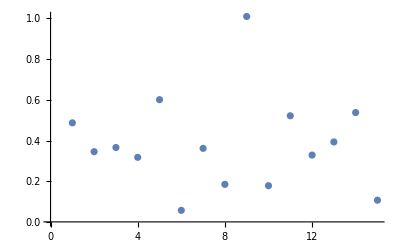

```mathematica
A=Sort[Log[N[Eigenvalues[U]]]/-I,Re[#1]>Re[#2]&];
LS=ConstantArray[0,{Length@A-1}];
For[n=1,n<Length@A,n++,LS[[n]]=A[[n]]-A[[n+1]]]
ListPlot[LS]
```

Secondly we attempt with CNOT and RevCNOT

```mathematica
θ=Pi/4;
XRow=SparseArray@KroneckerProduct[RX[θ],RX[θ],RX[θ],RX[θ]];
ZRow=SparseArray@KroneckerProduct[RZ[θ],RZ[θ],RZ[θ],RZ[θ]];
UOdd=SparseArray@KroneckerProduct[RevCNOT.CNOT,RevCNOT.CNOT];
UEven=SparseArray@KroneckerProduct[IdentityMatrix[2],RevCNOT.CNOT,IdentityMatrix[2]];
U=SparseArray@XRow.ZRow.UEven.ZRow.XRow.ZRow.UOdd.ZRow;
```

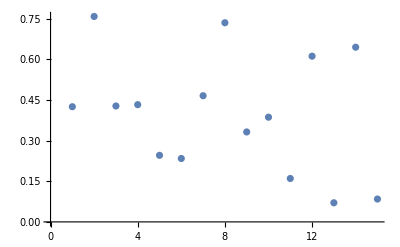

```mathematica
A=Sort[Log[N[Eigenvalues[U]]]/-I,Re[#1]>Re[#2]&];
LS=ConstantArray[0,{Length@A-1}];
For[n=1,n<Length@A,n++,LS[[n]]=A[[n]]-A[[n+1]]]
ListPlot[LS]
```